```mathematica
B[i_,n_,t_]:= Factorial[n]/(Factorial[i]*Factorial[n-i])*t^i*(1-t)^(n-i)
```

```mathematica
B[n_]:=Plot[Evaluate[Table[B[i,n,t],{i,0,n}]],{t,0,1},PlotRange->{{0,1},{0,1}}]
```

```mathematica
R[t_,P_]:= ∑_(i=0)^(Length[P]-1) P[[i+1]]B[i,Length[P]-1,t]
```

```mathematica
point={};
pts={};
line = {};
arrow={};
DynamicModule[{c={}},ClickPane[Framed@Graphics[{Black,Point[Dynamic[pts]],Red,Point[{Dynamic[point]}],Line[Dynamic[line]],Arrow[Dynamic[arrow],0.4]},PlotRange->10],(If[Length[pts]<10,AppendTo[pts,#],pts={#}];)&]]
```

```mathematica
length;
P =pts;
line = {};
step = 0.0002;
length = Length[P];
lengthl;
t=0;
While[t< 1,
t+= step;
point =R[t,P];
AppendTo[line,point];
lengthl = Length[line];
If[lengthl≥ 2,arrow={line[[lengthl-1]],line[[lengthl]]}];

];
Clear[t];
```

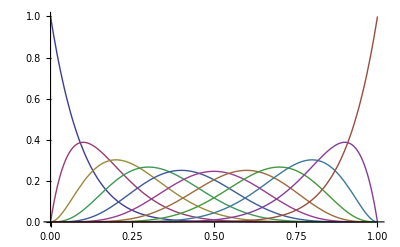

```mathematica
B[10]
```